18683

302800

12898

195927

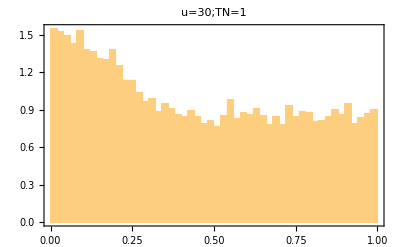
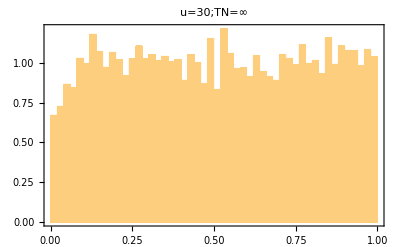

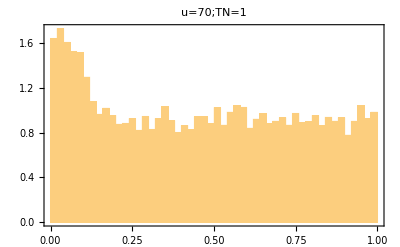
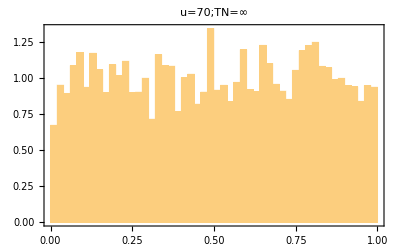

```mathematica
data1=ReadList["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\bond_freq_TNtransition1_L500T100000_u30t1.txt",Number];
Length[data1]

datam1=ReadList["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\bond_freq_TNtransition100000_L500T100000_u30t1.txt",Number];
Length[datam1]
data7=ReadList["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\bond_freq_TNtransition1_L500T100000_u70t1.txt",Number];
Length[data7]
datam7=ReadList["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\bond_freq_TNtransition100000_L500T100000_u70t1.txt",Number];
Length[datam7]
{Histogram[(Log@data1-Log[1])/30,{0.02},"PDF",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["u=30;TN=1",14]],Histogram[(Log@datam1-Log[1])/30,{0.02},"PDF",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["u=30;TN=∞",14]]}
{Histogram[(Log@data7-Log[1])/70,{0.02},"PDF",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["u=70;TN=1",14]],
Histogram[(Log@datam7-Log[1])/70,{0.02},"PDF",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["u=70;TN=∞",14]]}
```